## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="DHQS";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp.csv";

mainFolder = "fit_DHQS_TEST_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{2dda7p,Km or S05 substrate}

{5.7×10^-6,Km or S05 value}

{{{2dda7p,Null}},kcat substrates}

{16,kcat value}

{2dda7p,Km or S05 substrate}

{6.×10^-7,Km or S05 value}

{2dda7p,Km or S05 substrate}

{5.5×10^-6,Km or S05 value}

{2dda7p,Km or S05 substrate}

{0.0000415,Km or S05 value}

{2dda7p,Km or S05 substrate}

{0.00005,Km or S05 value}

{3-deoxy-D-arabinoheptulosonate7-phosphonate,Inhibition or activation constant substrate}

{2.5×10^-6,Inhibition or activation constant value}

{3-deoxy-D-arabinoheptulosonate7-homophosphonate,Inhibition or activation constant substrate}

{0.00026,Inhibition or activation constant value}

{D-gluco-heptulosonate7-phosphate,Inhibition or activation constant substrate}

{0.00008,Inhibition or activation constant value}

{D-gluco-heptulosonate7-phosphonate,Inhibition or activation constant substrate}

{5.×10^-6,Inhibition or activation constant value}

{D-gluco-heptulosonate7-homophosphate,Inhibition or activation constant substrate}

{0.0012,Inhibition or activation constant value}

{2dda7p,Null;,Keq substrate}

{8.5×10^22,Keq value}

((2dda7p)^c⇌(3dhq)^c+pi^c)^DHQS

Null;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2dda7p,Null; | 8.5×10^22 | 8.075×10^22
8.925×10^22 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2dda7p | 5.7×10^-6 | 5.5×10^-6
5.9×10^-6 |  | M | 6.8 | 25 |  | 
1 | 2dda7p | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 |  | M | 6.5 | 20 |  | 
1 | 2dda7p | 5.5×10^-6 | 5.225×10^-6
5.775×10^-6 |  | M | 8.5 | 20 |  | 
1 | 2dda7p | 0.0000415 | 0.000039425
0.000043575 |  | M | 7.4 | 15 |  | 
1 | 2dda7p | 0.00005 | 0.0000475
0.0000525 |  | M | 7.5 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2dda7p | Null | 16 | 15.8
16.2 | 1/s | 6.8 | 25 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | 3-deoxy-D-arabinoheptulosonate7-phosphonate | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 |  |  | M | 7.5 | 25 |  | 
1 | Kic | 3-deoxy-D-arabinoheptulosonate7-homophosphonate | 0.00026 | 0.000247
0.000273 |  |  | M | 7.5 | 25 |  | 
1 | Kic | D-gluco-heptulosonate7-phosphate | 0.00008 | 0.000076
0.000084 |  |  | M | 7.5 | 25 |  | 
1 | Kic | D-gluco-heptulosonate7-phosphonate | 5.×10^-6 | 4.75×10^-6
5.25×10^-6 |  |  | M | 7.5 | 25 |  | 
1 | Kic | D-gluco-heptulosonate7-homophosphate | 0.0012 | 0.00114
0.00126 |  |  | M | 7.5 | 25 |  |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,0,0};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities = {0,0,0,0,0};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2dda7p)^c⇌(3dhq)^c+pi^c)^DHQS

Null;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2dda7p,Null; | 8.5×10^22 | 8.075×10^22
8.925×10^22 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2dda7p | 5.7×10^-6 | 5.5×10^-6
5.9×10^-6 |  | M | 6.8 | 25 |  | 
1 | 2dda7p | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 |  | M | 6.5 | 20 |  | 
1 | 2dda7p | 5.5×10^-6 | 5.225×10^-6
5.775×10^-6 |  | M | 8.5 | 20 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2dda7p | Null | 16 | 15.8
16.2 | 1/s | 6.8 | 25 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_DHQS[c] + 2dda7p[c] <=> E_DHQS[c]&2dda7p",
				"E_DHQS[c]&2dda7p <=> E_DHQS[c]&3dhq&pi",
				"E_DHQS[c]&3dhq&pi <=> E_DHQS[c]&3dhq + pi[c]",
				"E_DHQS[c]&3dhq <=> E_DHQS[c] + 3dhq[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((DHQS^c)_^+(2dda7p)^c⇌(DHQS^c&(2dda7p)^c)_^)^DHQS1,((DHQS^c&(3dhq)^c)_^⇌(DHQS^c)_^+(3dhq)^c)^DHQS2,((DHQS^c&(2dda7p)^c)_^⇌(DHQS^c&(3dhq)^c&pi^c)_^)^DHQS3,((DHQS^c&(3dhq)^c&pi^c)_^⇌(DHQS^c&(3dhq)^c)_^+pi^c)^DHQS4}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((DHQS^c)_^+(2dda7p)^c⇌(DHQS^c&(2dda7p)^c)_^)^DHQS1,Overscript[(DHQS^c&(3dhq)^c)_^⇌(DHQS^c)_^+(3dhq)^c, DHQS2],((DHQS^c&(2dda7p)^c)_^⇌(DHQS^c&(3dhq)^c&pi^c)_^)^DHQS3,Overscript[(DHQS^c&(3dhq)^c&pi^c)_^⇌(DHQS^c&(3dhq)^c)_^+pi^c, DHQS4]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(2dda7p)^c→0}

{(3dhq)^c→0,pi^c→0}

{(2dda7p)^c→∞}

{(3dhq)^c→∞,pi^c→∞}

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={(*{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}*)};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	2dda7p[c]	3dhq[c]	pi[c]	param_DHQS_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt"	8.5e22
1	5.7e-7	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.09090909090909094
1	9.033891197028351e-7	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.13680688860321008
1	1.431775265960462e-6	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.20076000891310194
1	2.2692108721549328e-6	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.2847472489508013
1	3.5964568635371007e-6	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.3868631798468569
1	5.7000000000000005e-6	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.5000000000000001
1	9.033891197028351e-6	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.6131368201531432
1	0.000014317752659604621	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.7152527510491989
1	0.000022692108721549327	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.7992399910868981
1	0.000035964568635371005	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.8631931113967899
1	0.00005700000000000001	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.9090909090909092
1	6.000000000000003e-8	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.09090909090909097
1	9.50935915476669e-8	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.1368068886032101
1	1.50713185890575e-7	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.20076000891310194
1	2.3886430233209827e-7	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.28474724895080133
1	3.78574406688116e-7	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.386863179846857
1	6.000000000000003e-7	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.5000000000000001
1	9.50935915476669e-7	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.6131368201531433
1	1.50713185890575e-6	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.7152527510491988
1	2.388643023320983e-6	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.7992399910868984
1	3.78574406688116e-6	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.8631931113967901
1	6.000000000000003e-6	0	0	1	6.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.9090909090909092
1	5.500000000000003e-7	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.09090909090909095
1	8.716912558536133e-7	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.13680688860321014
1	1.381537537330271e-6	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.20076000891310197
1	2.1895894380442344e-6	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.2847472489508014
1	3.4702653946410634e-6	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.38686317984685703
1	5.500000000000003e-6	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.5000000000000001
1	8.716912558536133e-6	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.6131368201531433
1	0.00001381537537330271	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.7152527510491989
1	0.000021895894380442343	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.7992399910868981
1	0.000034702653946410634	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.8631931113967901
1	0.000055000000000000036	0	0	1	8.5	20	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt"	0.9090909090909093
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16
1	0.01	0	0	1	6.8	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt"	16

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateRev_3dhq.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateRev_pi.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateFor_2dda7p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateRev_3dhq.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/relRateRev_pi.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_DHQS_TEST_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 2.32303007419
best_fit: 2.32303007444
best_fit: 2.32303007954
best_fit: 2.32303042771
best_fit: 2.32303007557

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | haldaneRatio_1 | 7.75825×10^-7 | 6.01905×10^-13 | 1.51844×10^17 | 0.00017864 | 8.5×10^22 | 8.49998×10^22
1 | relRateFor_2dda7p | 0.456447 | 0.208343 | 0.169139 | 186.053 | 0.0909091 | 0.260048
1 | relRateFor_2dda7p | 0.417456 | 0.174269 | 0.22093 | 161.49 | 0.136807 | 0.357737
1 | relRateFor_2dda7p | 0.368375 | 0.1357 | 0.268109 | 133.547 | 0.20076 | 0.468869
1 | relRateFor_2dda7p | 0.311342 | 0.0969336 | 0.298431 | 104.805 | 0.284747 | 0.583178
1 | relRateFor_2dda7p | 0.250784 | 0.0628924 | 0.30233 | 78.1491 | 0.386863 | 0.689193
1 | relRateFor_2dda7p | 0.192281 | 0.036972 | 0.278486 | 55.6973 | 0.5 | 0.778486
1 | relRateFor_2dda7p | 0.140732 | 0.0198054 | 0.234655 | 38.2712 | 0.613137 | 0.847792
1 | relRateFor_2dda7p | 0.0989364 | 0.00978842 | 0.182995 | 25.5846 | 0.715253 | 0.898247
1 | relRateFor_2dda7p | 0.0673411 | 0.00453482 | 0.134054 | 16.7726 | 0.79924 | 0.933294
1 | relRateFor_2dda7p | 0.0447353 | 0.00200125 | 0.0936557 | 10.8499 | 0.863193 | 0.956849
1 | relRateFor_2dda7p | 0.0292076 | 0.000853086 | 0.0632419 | 6.95661 | 0.909091 | 0.972333
1 | relRateFor_2dda7p | 0.406257 | 0.165044 | 0.0552352 | 60.7587 | 0.0909091 | 0.0356739
1 | relRateFor_2dda7p | 0.392726 | 0.154234 | 0.0814232 | 59.5169 | 0.136807 | 0.0553837
1 | relRateFor_2dda7p | 0.37314 | 0.139234 | 0.115737 | 57.6494 | 0.20076 | 0.0850231
1 | relRateFor_2dda7p | 0.346 | 0.119716 | 0.156378 | 54.9183 | 0.284747 | 0.128369
1 | relRateFor_2dda7p | 0.310539 | 0.0964347 | 0.197621 | 51.0829 | 0.386863 | 0.189242
1 | relRateFor_2dda7p | 0.267544 | 0.0715795 | 0.229961 | 45.9922 | 0.5 | 0.270039
1 | relRateFor_2dda7p | 0.219818 | 0.0483202 | 0.243531 | 39.7188 | 0.613137 | 0.369606
1 | relRateFor_2dda7p | 0.171718 | 0.0294872 | 0.233592 | 32.6587 | 0.715253 | 0.481661
1 | relRateFor_2dda7p | 0.127729 | 0.0163148 | 0.203649 | 25.4804 | 0.79924 | 0.595591
1 | relRateFor_2dda7p | 0.0909649 | 0.00827462 | 0.163121 | 18.8973 | 0.863193 | 0.700073
1 | relRateFor_2dda7p | 0.0625194 | 0.00390867 | 0.121886 | 13.4074 | 0.909091 | 0.787205
1 | relRateFor_2dda7p | 0.444915 | 0.19795 | 0.162325 | 178.558 | 0.0909091 | 0.253234
1 | relRateFor_2dda7p | 0.407429 | 0.165999 | 0.212766 | 155.523 | 0.136807 | 0.349572
1 | relRateFor_2dda7p | 0.360067 | 0.129648 | 0.259225 | 129.122 | 0.20076 | 0.459985
1 | relRateFor_2dda7p | 0.304808 | 0.0929081 | 0.289723 | 101.748 | 0.284747 | 0.574471
1 | relRateFor_2dda7p | 0.245903 | 0.0604681 | 0.294628 | 76.1581 | 0.386863 | 0.681491
1 | relRateFor_2dda7p | 0.188797 | 0.0356442 | 0.272266 | 54.4531 | 0.5 | 0.772266
1 | relRateFor_2dda7p | 0.138335 | 0.0191365 | 0.229988 | 37.5101 | 0.613137 | 0.843125
1 | relRateFor_2dda7p | 0.0973325 | 0.00947361 | 0.179683 | 25.1216 | 0.715253 | 0.894936
1 | relRateFor_2dda7p | 0.0662889 | 0.00439421 | 0.131795 | 16.4901 | 0.79924 | 0.931035
1 | relRateFor_2dda7p | 0.0440544 | 0.00194079 | 0.0921566 | 10.6762 | 0.863193 | 0.95535
1 | relRateFor_2dda7p | 0.0287709 | 0.000827766 | 0.0622647 | 6.84911 | 0.909091 | 0.971356
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.
1 | absRateFor | 1.13802×10^-6 | 1.29509×10^-12 | 0.0000419263 | 0.000262039 | 16 | 16.

### Simulated Data and Best Fit Data Plot

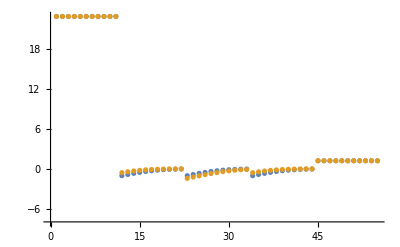

-Graphics-

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

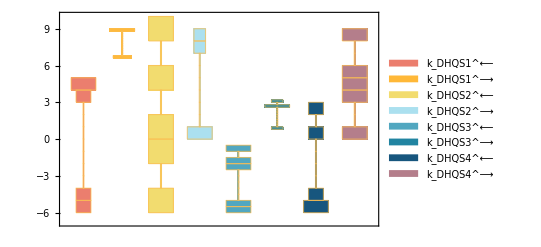

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

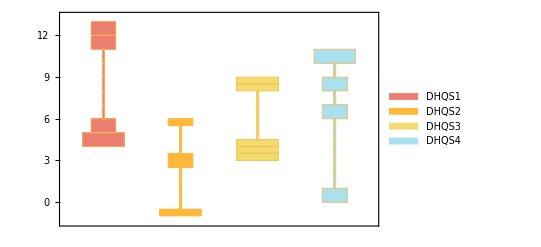

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

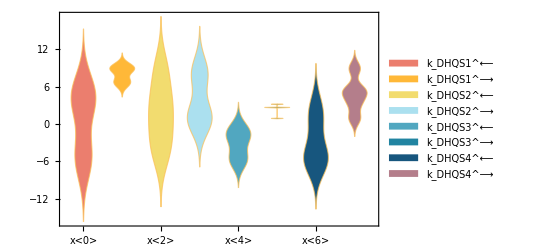

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

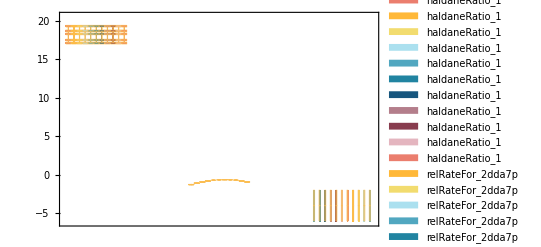

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
5.7×10^-6 | 1.6219×10^-6 | 71.5456
6.×10^-7 | 1.6219×10^-6 | 170.317
5.5×10^-6 | 1.6219×10^-6 | 70.5109

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
16 | 16. | 0.000262039

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

data value | predicted value | error in %
{}⟦1⟧⟦3⟧ | 1 | (100 Abs[-1+{}⟦1⟧⟦3⟧])/({}⟦1⟧⟦3⟧)

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
8.5×10^22 | 8.49998×10^22 | 0.00017864